```mathematica
<<IntervalTools`
```

Apparently,  Griewank suggested the following function as a test problem for global optimization. We get rigorous bounds on the minimum  without even caring about using the symmetry.

```mathematica
Clear[x,y]
f[x_,y_]=(x^2+y^2)/4000+(Cos[x] Cos[y])/(√2)+1
```

1+(x^2+y^2)/4000+(Cos[x] Cos[y])/(√2)

```mathematica
f[RealInterval,RealInterval]
N[%]
```

Interval[{1-1/(√2),∞}]

Interval[{0.292893,∞}]

```mathematica
AbsoluteTiming[{bds,where}=RigorousMinimize[f,f,{RealInterval,RealInterval}];]
{bds,N[bds]}
```

{0.401138,Null}

{Interval[{16818548041/16777216000+Cos[12859/4096]/(√2),10763874861/10737418240+(Cos[1/8192] Cos[12859/4096])/(√2)}],Interval[{0.295358,0.295359}]}

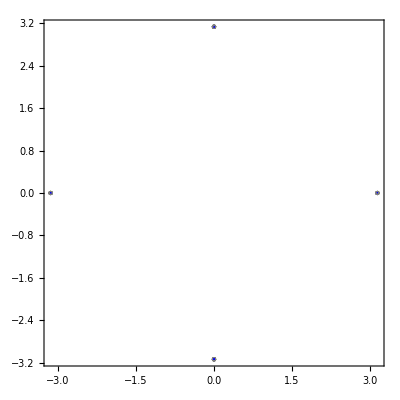

```mathematica
Show[IntervalGraphics[where,{4Interval[{-1,1}],4Interval[{-1,1}]}],Frame->True]
```

Okay, I need to work on that visualization!

```mathematica
where//N
```

{{Interval[{-3.14038,-3.14014}],Interval[{-0.000488281,0.000488281}]},{Interval[{-3.14014,-3.13989}],Interval[{-0.000976563,0.000732422}]},{Interval[{-3.13989,-3.13965}],Interval[{-0.000976563,0.000976563}]},{Interval[{-3.13965,-3.1394}],Interval[{-0.0012207,0.0012207}]},{Interval[{-3.1394,-3.13916}],Interval[{-0.000976563,0.000976563}]},{Interval[{-3.13916,-3.13892}],Interval[{-0.00109863,0.000976563}]},{Interval[{-3.13892,-3.13879}],Interval[{0.000488281,0.000732422}]},{Interval[{-3.13892,-3.13867}],Interval[{-0.000732422,0.000488281}]},{Interval[{-3.13867,-3.13843}],Interval[{-0.000488281,0.000488281}]},{Interval[{-0.0012207,-0.000976562}],Interval[{-3.13965,-3.1394},{3.1394,3.13965}]},{Interval[{-0.00109863,-0.000976562}],Interval[{-3.1394,-3.13892}]},{Interval[{-0.000976563,-0.000854492}],Interval[{-3.13892,-3.13867},{3.13892,3.13916}]},{Interval[{-0.000976563,-0.000732422}],Interval[{-3.13965,-3.13916},{3.13916,3.13989}]},{Interval[{-0.000976563,-0.000488281}],Interval[{-3.14014,-3.13965}]},{Interval[{-0.000854492,-0.000732422}],Interval[{-3.13892,-3.13867},{3.13892,3.13916}]},{Interval[{-0.000732422,-0.000610352}],Interval[{3.13867,3.13892}]},{Interval[{-0.000732422,-0.000488281}],Interval[{-3.13965,-3.13879},{3.13892,3.14014}]},{Interval[{-0.000610352,-0.000488281}],Interval[{3.13867,3.13892}]},{Interval[{-0.000488281,-0.000244141}],Interval[{-3.14014,-3.13916},{-3.13867,-3.13855},{3.13855,3.13867},{3.13916,3.14014}]},{Interval[{-0.000488281,2.22507×10^-308}],Interval[{-3.14038,-3.14014},{-3.13916,-3.13867},{3.13867,3.13916},{3.14014,3.14038}]},{Interval[{-0.000244141,2.22507×10^-308}],Interval[{-3.14014,-3.13916},{-3.13867,-3.13843},{3.13843,3.13867},{3.13916,3.14014}]},{Interval[{-2.22507×10^-308,0.000244141}],Interval[{-3.14014,-3.13916},{-3.13867,-3.13843},{3.13843,3.13916}]},{Interval[{-2.22507×10^-308,0.000488281}],Interval[{-3.14038,-3.14014},{-3.13916,-3.13867},{3.13916,3.14038}]},{Interval[{0.000244141,0.000366211}],Interval[{-3.13867,-3.13843},{3.13843,3.13867}]},{Interval[{0.000244141,0.000488281}],Interval[{-3.14014,-3.13916},{3.13867,3.13916}]},{Interval[{0.000366211,0.000488281}],Interval[{-3.13867,-3.13843},{3.13843,3.13867}]},{Interval[{0.000488281,0.000732422}],Interval[{-3.13965,-3.13879},{3.13879,3.13965}]},{Interval[{0.000488281,0.000976563}],Interval[{-3.14014,-3.13965},{3.13965,3.14014}]},{Interval[{0.000732422,0.000854492}],Interval[{3.13867,3.13892}]},{Interval[{0.000732422,0.000976563}],Interval[{-3.13965,-3.13916},{3.13916,3.13965}]},{Interval[{0.000854492,0.000976563}],Interval[{3.13867,3.13892}]},{Interval[{0.000976562,0.00109863}],Interval[{-3.1394,-3.13892},{3.13892,3.1394}]},{Interval[{0.000976562,0.0012207}],Interval[{-3.13965,-3.1394},{3.1394,3.13965}]},{Interval[{3.13843,3.13867}],Interval[{-0.000244141,0.000488281}]},{Interval[{3.13855,3.13867}],Interval[{-0.000488281,-0.000244141}]},{Interval[{3.13867,3.13892}],Interval[{-0.000976563,0.000976563}]},{Interval[{3.13892,3.13916}],Interval[{-0.00109863,-0.000976562},{-0.000732422,0.000732422},{0.000976562,0.00109863}]},{Interval[{3.13916,3.1394}],Interval[{-0.000976563,0.00109863}]},{Interval[{3.1394,3.13965}],Interval[{-0.0012207,0.0012207}]},{Interval[{3.13965,3.13989}],Interval[{-0.000976563,0.000976563}]},{Interval[{3.13989,3.14014}],Interval[{-0.000732422,0.000976563}]},{Interval[{3.14014,3.14038}],Interval[{-0.000488281,0.000488281}]}}

```mathematica
AbsoluteTiming[{bds,where}=RigorousMinimize[f,f,{RealInterval,RealInterval}];]
{bds,N[bds]}
```

{0.372895,Null}

{Interval[{16818548041/16777216000+Cos[12859/4096]/(√2),10763874861/10737418240+(Cos[1/8192] Cos[12859/4096])/(√2)}],Interval[{0.295358,0.295359}]}